# Fisher two - period optimal consumption problem

```mathematica
SetDirectory[NotebookDirectory[]]
```

~/Choice/LectureNotes/Consumption/Handouts/2PeriodLCModel/Software/Mathematica

## Lifetime income is earned in the first period of life

### Parameter definition

```mathematica
Y1=1;(* First period income *)
```

### Functional forms

#### Intertemporal budget constraint and indifference curve

Intertemporal budget constraint

```mathematica
IBC[R_,C1_,Y1_]:=(Y1-C1)R
```

Indifference curve: C2 given C1 which keeps the value function at a constant level V = C1^(1-ρ)/(1-ρ)+β C2^(1-ρ)/(1-ρ)

```mathematica
IndCurve[V_,C1_]:=If[((V(1-ρ)-C1^(1-ρ))/β)^(1/(1-ρ))>0,((V(1-ρ)-C1^(1-ρ))/β)^(1/(1-ρ))];
```

#### Optimal solution

Optimal C1 (using IBC and Euler equation)

```mathematica
C1[R_]:=R/(R+(R β)^(1/ρ))Y1
```

Optimal C2 (using Euler equation)

```mathematica
C2[R_]:=C1[R](R β)^(1/ρ)
```

Value function at the optimal C1 and C2

```mathematica
V[R_]:=C1[R]^(1-ρ)/(1-ρ)+β C2[R]^(1-ρ)/(1-ρ)
```

#### Substitution effect

Optimal C1 with only substitution effect obtained by using the Indifference curve and Euler equation: V[RHi] = C1Subs^(1-ρ)/^(1-ρ)+ β((C1Subs(RLo β)^(1/ρ))^(1-ρ))/^(1-ρ)

```mathematica
C1Subs=((V[RHi](1-ρ))/(1+β(RLo β)^((1-ρ)/ρ)))^(1/(1-ρ));
```

Optimal C2 with only substitution effect (using the Euler equation)

```mathematica
C2Subs=C1Subs(RLo β)^(1/ρ);
```

First period income which allows the consumer under RLo to achieve the same utility obtainable under RHi and Y1 (using IBC), equivalent variation

```mathematica
Y1Equiv=C1Subs+C2Subs/RLo;
```

### General parameter definition

```mathematica
RLo=1 ;(* Low interest rate *)
RHi=2 ;(* High interest rate *)
ρ=2; (* CRRA coefficient *)
β=0.96(* Intertemporal discount factor *);
```

### Plot

This plot is flexible to the initial parameter definition.

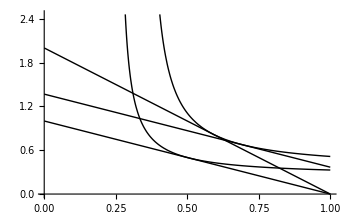

```mathematica
Plot[{IBC[RLo,C,Y1],IndCurve[V[RLo],C],IBC[RHi,C,Y1],IndCurve[V[RHi],C],IBC[RLo,C,Y1Equiv]},{C,0,Y1}, PlotStyle->Black]
```

Finalizing the plot : this part of the code has to be modified according the initial parameter definition.

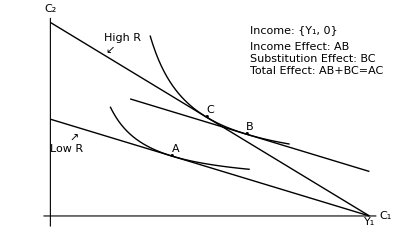

```mathematica
Y1Plot=Show[
Plot[{IBC[RLo,C,Y1],IBC[RHi,C,Y1]},{C,0.2,Y1}, PlotStyle->Black] ,
Plot[IBC[RLo,C,Y1Equiv],{C,.4,1}, PlotStyle->Black],
Plot[IndCurve[V[RLo],C],{C,0.35,0.7}, PlotStyle->Black] ,
Plot[IndCurve[V[RHi],C],{C,0.45,0.8}, PlotStyle->Black] ,Graphics[{Text["Income: {Y_1, 0}",{.7,1.54},{-1,0}],Text["Income Effect: AB",{.7,1.4},{-1,0}],Text["Substitution Effect: BC",{.7,1.3},{-1,0}],Text["Total Effect: AB+BC=AC",{.7,1.2},{-1,0}],
Text[Style["•",Large],{C1[RLo],C2[RLo]}],Text["A",{C1[RLo]+0.01,C2[RLo]+0.06}],
Text[Style["•",Large],{C1[RHi],C2[RHi]}],Text["C",{C1[RHi]+0.01,C2[RHi]+0.06}],
Text[Style["•",Large],{C1Subs,C2Subs}],Text["B",{C1Subs+0.01,C2Subs+0.06}],
Text["High R",{.38,1.47}],Text[Style["↙",Large],{.35,1.37}],Text["Low R",{.24,.55}],Text[Style["↗",Large],{.26,.64}],
Text["Y_1",{Y1,-0.05}]
}],Ticks->None,AxesLabel->{"C_1","C_2"},ImageSize->{580},BaseStyle->{FontSize->15},PlotRange->{-0.05,1.6}]
```

```mathematica
Export["../../Figures/FisherFigureY1.eps",Y1Plot];
Export["../../Figures/FisherFigureY1.pdf",Y1Plot];Export["../../Figures/FisherFigureY1.dat",Y1Plot];Export["../../Figures/FisherFigureY1.png",Y1Plot];
```

## Lifetime income is earned in the second period of life

### Parameter definition

```mathematica
Y2=1 ;(* Second period income *)
```

### Functional forms

#### Intertemporal budget constraint and indifference curve

Intertemporal budget constraint

```mathematica
IBC[R_,C1_,Y2_]:=Y2-C1 R
```

Indifference curve: C2 given C1 which keeps the value function at a constant level V = C1^(1-ρ)/(1-ρ)+β C2^(1-ρ)/(1-ρ)

```mathematica
IndCurve[V_,C1_]:=If[((V(1-ρ)-C1^(1-ρ))/β)^(1/(1-ρ))>0,((V(1-ρ)-C1^(1-ρ))/β)^(1/(1-ρ))]
```

#### Optimal solution

Optimal C1 (using IBC and Euler equation)

```mathematica
C1[R_]:=Y2/(R+(R β)^(1/ρ))
```

Optimal C2 (using Euler equation)

```mathematica
C2[R_]:=C1[R](R β)^(1/ρ)
```

Value function at the optimal C1 and C2

```mathematica
V[R_]:=C1[R]^(1-ρ)/(1-ρ)+β C2[R]^(1-ρ)/(1-ρ)
```

#### Substitution effect

Optimal C1 with only substitution effect obtained by using the Indifference curve and Euler equation: V[RHi] = C1Subs^(1-ρ)/^(1-ρ)+ β((C1Subs(RLo β)^(1/ρ))^(1-ρ))/^(1-ρ)

```mathematica
C1Subs=((V[RHi](1-ρ))/(1+β(RLo β)^((1-ρ)/ρ)))^(1/(1-ρ));
```

Optimal C2 with only substitution effect (using the Euler equation)

```mathematica
C2Subs=C1Subs(RLo β)^(1/ρ);
```

Second period income which allows the consumer under RLo to achieve the same utility obtainable under RHi and Y2 (using IBC), equivalent variation

```mathematica
Y2Equiv=C1Subs RLo+C2Subs;
```

#### Human wealth effect

Second period income with present discounted value under RLo equal to the present discounted value of Y2 under RHi (using IBC)

```mathematica
Y2HW = Y2 RLo/RHi ;
```

Optimal C1 with only human wealth effect (using IBC and Euler equation)

```mathematica
C1HW=Y2HW/(RLo+(RLo β)^(1/ρ));
```

Optimal C2 with only human wealth effect (using Euler equation)

```mathematica
C2HW=C1HW(RLo β)^(1/ρ);
```

Value function at the optimal C1 and C2 with only human wealth effect

```mathematica
VHW=C1HW^(1-ρ)/(1-ρ)+β C2HW^(1-ρ)/(1-ρ);
```

### Plot

This plot is flexible to the initial parameter definition.

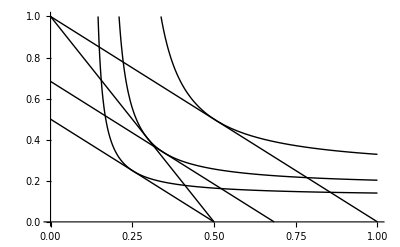

```mathematica
Plot[{IBC[RLo,C,Y2],IndCurve[V[RLo],C],IBC[RHi,C,Y2],IndCurve[V[RHi],C],IBC[RLo,C,Y2HW],IndCurve[VHW,C],IBC[RLo,C,Y2Equiv]},{C,0,Y2/RLo}, PlotStyle->Black,PlotRange->{0,Y2}]
```

Finalizing the plot : this part of the code has to be modified according the initial parameter definition.

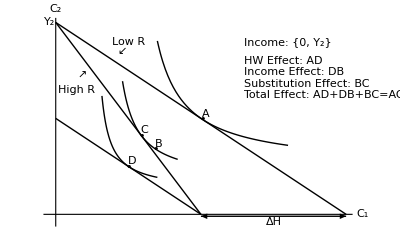

```mathematica
Y2Plot=Show[
Plot[{IBC[RLo,C,Y2]},{C,0,1}, PlotStyle->Black] ,
Plot[{IBC[RHi,C,Y2],IBC[RLo,C,Y2HW]},{C,0,Y2/RHi}, PlotStyle->Black],
Plot[IndCurve[V[RLo],C],{C,0.35,0.8}, PlotStyle->Black] ,
Plot[IndCurve[V[RHi],C],{C,0.23,.42}, PlotStyle->Black] ,
Plot[IndCurve[VHW,C],{C,0.15,.35}, PlotStyle->Black] ,Graphics[{Text["Income: {0, Y_2}",{.65,0.9},{-1,0}],Text["HW Effect: AD",{.65,0.8},{-1,0}],Text["Income Effect: DB",{.65,0.74},{-1,0}],Text["Substitution Effect: BC",{.65,0.68},{-1,0}],Text["Total Effect: AD+DB+BC=AC",{.65,.62},{-1,0}],
Text[Style["•",Large],{C1[RLo],C2[RLo]}],Text["A",{C1[RLo]+0.01,C2[RLo]+0.03}],
Text[Style["•",Large],{C1[RHi],C2[RHi]}],Text["C",{C1[RHi]+0.01,C2[RHi]+0.03}],
Text[Style["•",Large],{C1Subs,C2Subs}],Text["B",{C1Subs+0.01,C2Subs+0.03}],
Text[Style["•",Large],{C1HW,C2HW}],Text["D",{C1HW+0.01,C2HW+0.03}],
Text["High R",{.07,.65}],Text[Style["↗",Large],{.09,.72}],Text["Low R",{.25,.9}],Text[Style["↙",Large],{.23,.85}],
Text["ΔH",{Y2/RHi+(Y2/RLo-Y2/RHi)/2,-.04}],
Text["Y_2",{-.02,Y2}]
}],
Graphics[{Arrowheads[{-.03,.03}],Arrow[{{Y2/RHi,-0.01},{Y2/RLo,-0.01}}]}]
,Ticks->None,AxesLabel->{"C_1","C_2"},ImageSize->{580},BaseStyle->{FontSize->15},PlotRange->{-0.04,Y2}]
```

```mathematica
Export["../../Figures/FisherFigureY2.eps",Y2Plot];
Export["../../Figures/FisherFigureY2.pdf",Y2Plot];
Export["../../Figures/FisherFigureY2.png",Y2Plot];
```